### Def

Ordering so that small (abs) numbers come first, then short symbols, then long, and zero last.

```mathematica
Clear[rankA]
```

```mathematica
rankA[0]={3,0};
rankA[Except[0,xx_]]:=If[NumericQ[x],{1,Abs[x]},{2,LeafCount[xx]}];
pivotOrder[aa_,bb_]:=Module[{ra=rankA[aa],rb=rankA[bb]},Which[ra⟦1⟧<rb⟦1⟧,1,ra⟦1⟧>rb⟦1⟧,-1,ra⟦2⟧<rb⟦2⟧,1,ra⟦2⟧>rb⟦2⟧,-1,True,0]]
(*pivotOrder[aa_,bb_]:=Which[aa===bb,0,aa===0,-1,¬NumberQ[aa],If[¬NumberQ[bb],LeafCount[aa]≤LeafCount[bb],If[bb===0,1,-1]],bb===0∨¬NumberQ[bb],1,True,Abs[aa]≤Abs[bb]]*)
```

Ordering so that zero vector comes first, then according to best (minimal) elements in two rows.

```mathematica
rankB[{0..}]:={0,0};
rankB[Except[{0..},v_]]:=rankA[Sort[v,pivotOrder]⟦1⟧]
rowOrder[rr1_,rr2_]:=Module[{ra=rankB[rr1],rb=rankB[rr2]},Which[ra⟦1⟧<rb⟦1⟧,1,ra⟦1⟧>rb⟦1⟧,-1,ra⟦2⟧<rb⟦2⟧,1,ra⟦2⟧>rb⟦2⟧,-1,True,0]]
```

Permutation in which zero columns come first, and the remaining are ordered according to the best (minimal) element in each.

```mathematica
numColSort[MM_]:=Ordering[MMᵀ,All,rowOrder]
```

Open dialog with buttons Yes/No/Proceed mapping to True/False/”cont”

```mathematica
contButt[]:=DialogInput[Column[{Style["Continue to the next row?",24],
Row[{DefaultButton[Style["Continue",20],DialogReturn[True]],CancelButton[Style["Abort",20],DialogReturn[False]],Button[Style["Stop asking",20],DialogReturn["cont"]]}]}],
ButtonBoxOptions->{ImageMargins->{{20,10},{10,40}},FrameMargins->5}(*,WindowFrame->"Normal",WindowSize->{500,150},WindowFrameElements->{"ResizeArea"}*)]
(*contButt[]:=ChoiceDialog[Style["Continue to the next row?",24],{Style["Continue",20]->True,Style["Abort",20]->False,Style["Stop asking",20]->"cont"},ButtonBoxOptions->{ImageMargins->{{20,20},{0,20}},FrameMargins->5}]*)
```

Print formatted output to a notebook.

```mathematica
extPrint[nn_,tt_]:=NotebookWrite[nn,Cell[BoxData@ToBoxes[tt],"Output"]]
```

```mathematica
MacieForm[MM_,OptionsPattern[Grid]]:=DisplayForm@StyleBox[RowBox[{"(",Grid[MM,Frame->OptionValue[Frame],FrameStyle->OptionValue[FrameStyle]],")"}],SpanMaxSize->Infinity]
```

Reduce by division to standard form with 1/0.

```mathematica
cleanUp[MM_]:=Module[{row,R={},p,k},
Do[If[MatchQ [row,{0..}],AppendTo[R,row];Break[]];
p=FirstPosition[row,Except[0],Heads->False]⟦1⟧;AppendTo[R,row/row⟦p⟧];
Do[R⟦k⟧=R⟦k⟧-R⟦-1⟧R⟦k,p⟧,{k,1,Length[R]-1}];
,{row,MM}];
R]
```

Inverse permutation

```mathematica
invPerm[LL_]:=Table[Position[LL,k$1]⟦1,1⟧,{k$1,Length[LL]}]
```

Gaussian Elimination.

```mathematica
GaussElim[M_]:=Module[{𝓃=Dimensions[M],Μ={M},offset=0,den=1,shifty,fullPermu,blockPermu,shiftFo,sortFo,tmp,msg,shmsg="",i,j,k,nb,stat=True},
fullPermu=Array[#2&,{2,𝓃⟦2⟧}];nb=CreateDocument[Cell["Initial position: ⟦1,1⟧","Output"],WindowSize->Scaled[.5]];
Do[msg="Row: "<>ToString[k]<>". Denominator: "<>ToString[den]<>". ";shifty={};shmsg="";
blockPermu=numColSort[Μ⟦k,k;;,k+offset;;⟧];fullPermu⟦1⟧=Join[Range[k+offset-1],blockPermu+k+offset-1];
If[fullPermu⟦1⟧≠Range[𝓃⟦2⟧],Μ⟦k⟧=Μ⟦k,;;,fullPermu⟦1⟧⟧;fullPermu⟦2⟧=fullPermu⟦2,fullPermu⟦1⟧⟧;
msg=msg<>"Columns permuted: "<>ToString[fullPermu⟦1⟧]<>". "];
While[k≤𝓃⟦1⟧∧k+offset≤𝓃⟦2⟧∧MatchQ[Μ⟦k,k;;,k+offset⟧,{0..}],(*NOWE*)
AppendTo[shifty,{k,k+offset}];offset++;
shmsg="Shifted to column "<>ToString[k+offset]<>". "];msg=msg<>shmsg;
If[k>𝓃⟦1⟧∨k+offset>𝓃⟦2⟧,extPrint[nb,"Right wall reached, exitting."];Break[]];
shiftFo=MacieForm[MapAt[Style[#,Darker@Red]&,shifty]@Μ⟦k⟧,Frame->{None,None,{{k,𝓃⟦1⟧},{k+offset,k+offset}}->True},FrameStyle->Darker@Red];
Μ⟦k,k;;⟧=Sort[Μ⟦k,k;;⟧,pivotOrder[#1⟦k+offset⟧,#2⟦k+offset⟧]&];
sortFo=MacieForm[MapAt[Item[#,Frame->True,FrameStyle->Black]&,{k,k+offset}]@Μ⟦k⟧,Frame->{None,None,{{k+1,𝓃⟦1⟧},{k+offset,k+offset}}->True},FrameStyle->Darker@Green];
msg = msg<>"Sorted by col: "<>ToString[k+offset]<>". ";
AppendTo[Μ,Μ⟦k⟧];
Do[tmp=PolynomialReduce[Μ⟦k,k,k+offset⟧Μ⟦k,i,j⟧-Μ⟦k,i,k+offset⟧Μ⟦k,k,j⟧,den,{}];(*SEDNO Subscript[M, ij]-Subscript[M, il']/Subscript[M, ll'] Subscript[M, lj]*)
If[tmp⟦-1⟧=!=0,Print["Polynomial division eror: ",{Μ⟦k,k,k+offset⟧Μ⟦k,i,j⟧-Μ⟦k,i,k+offset⟧Μ⟦k,k,j⟧,den}];Abort[]];
Μ⟦k+1,i,j⟧=FullSimplify[tmp⟦1,1⟧];
,{i,k+1,𝓃⟦1⟧},{j,k+offset,𝓃⟦2⟧}];
den=Μ⟦k,k,k+offset⟧;
SelectionMove[nb,After,Notebook];extPrint[nb,msg];
Which[k+1≤𝓃⟦1⟧∧k+offset+1≤𝓃⟦2⟧,
extPrint[nb,Row[{ shiftFo,"⟶^SORT",sortFo,"⟶^REMOVE",MacieForm[MapAt[Item[#,Frame->True,FrameStyle->{Dashing[{1,1}],Lighter@Gray}]&,{{k,k+offset},{k+1,k+offset+1}}]@ Μ⟦k+1⟧,
Frame->{None,None,{{k,𝓃⟦1⟧},{k+offset,k+offset}}->True},FrameStyle->Directive[Dashing[{1,1}],Darker@Green]]}]],
k+1≤𝓃⟦1⟧,
extPrint[nb,Row[{ shiftFo,"⟶^SORT",sortFo,"⟶^REMOVE",MacieForm[MapAt[Item[#,Frame->True,FrameStyle->{Dashing[{1,1}],Lighter@Gray}]&,{k,k+offset}]@ Μ⟦k+1⟧,
Frame->{None,None,{{k+1,𝓃⟦1⟧},{k+offset,k+offset}}->True},FrameStyle->Directive[Dashing[{1,1}],Darker@Green]]}]],
True,
extPrint[nb,Row[{ shiftFo,"⟶^SORT",sortFo,"⟶^REMOVE",MatrixForm@MapAt[Item[#,Frame->True,FrameStyle->{Dashing[{1,1}],Lighter@Gray}]&,{k,k+offset}]@ Μ⟦k+1⟧}]]
];
If[stat=!="cont"∧k<𝓃⟦1⟧∧k+offset<𝓃⟦2⟧,stat=contButt[]];If[k==𝓃⟦1⟧∨k+offset==𝓃⟦2⟧∨stat=!=False,Continue[],Break[]];
,{k,1,𝓃⟦1⟧}];
extPrint[nb,Row[{"Standard form: ", MatrixForm@cleanUp[Μ⟦-1⟧],". Permutation matrix: ",MatrixForm@IdentityMatrix[𝓃⟦2⟧]⟦;;,fullPermu⟦2⟧⟧}]];
Print["Rank: ",Length[Select[Μ⟦-1⟧,#∪{0}=!={0}&]]];
CellPrint[ExpressionCell[IdentityMatrix[𝓃⟦2⟧]⟦;;,fullPermu⟦2⟧⟧,"Output"]];
Μ⟦-1⟧]
```

Proceed with elimination + assumptions until a symbolic denominator is found

```mathematica
stepGaussElim[M_,assu_]:=Module[{𝓃=Dimensions[M],Μ={M},offset=0,den=1,P,pivsol,fullPermu,blockPermu,tmp,i,j,k,status=True},
fullPermu=Array[#2&,{2,𝓃⟦2⟧}];
Do[
blockPermu=numColSort[Μ⟦k,k;;,k+offset;;⟧];fullPermu⟦1⟧=Join[Range[k+offset-1],blockPermu+k+offset-1];
If[fullPermu⟦1⟧≠Range[𝓃⟦2⟧],Μ⟦k⟧=Μ⟦k,;;,fullPermu⟦1⟧⟧;fullPermu⟦2⟧=fullPermu⟦2,fullPermu⟦1⟧⟧];
While[k≤𝓃⟦1⟧∧k+offset≤𝓃⟦2⟧∧MatchQ[Μ⟦k,k;;,k+offset⟧,{0..}],offset++];
If[k>𝓃⟦1⟧∨k+offset>𝓃⟦2⟧,Break[]];
Μ⟦k,k;;⟧=Sort[Μ⟦k,k;;⟧,pivotOrder[#1⟦k+offset⟧,#2⟦k+offset⟧]&];
AppendTo[Μ,Μ⟦k⟧];P=Μ⟦k,k,k+offset⟧;
If[¬NumericQ[P],pivsol=FullSimplify[Solve[P==0]];
(*Print["Symbolic pivot in row ",k,": ",P];
Print["Pivot sols: ",pivsol,FullSimplify[assu/.pivsol]];
Print["Ass ∧ Pivo=0? ",¬MatchQ[FullSimplify[assu/.pivsol],{False..}]];*)
If[¬MatchQ[FullSimplify[assu/.pivsol],{False..}],status=False;Break[]]];
Do[tmp=PolynomialReduce[Μ⟦k,k,k+offset⟧Μ⟦k,i,j⟧-Μ⟦k,i,k+offset⟧Μ⟦k,k,j⟧,den,Variables[den]];
If[tmp⟦-1⟧=!=0,Print["Polynomial division eror: ",{den,tmp}];Abort[]];
Μ⟦k+1,i,j⟧=FullSimplify[tmp⟦1,1⟧];
,{i,k+1,𝓃⟦1⟧},{j,k+offset,𝓃⟦2⟧}];
den=Μ⟦k,k,k+offset⟧;
,{k,1,𝓃⟦1⟧}];
If[status,𝔑=Simplify@NullSpace[Μ⟦-1⟧⟦invPerm[fullPermu⟦2⟧]⟧];(*Print["Completed successfully! Null space: ",𝔑];*),𝔑={}];
{P,status,𝔑}]
```

### Main

```mathematica
MatrixForm[ℳ={{-w[0],1,α2,α3},{0,-1-w[1],-2 α2,-2 α3},{0,-2,-α2-w[2],-2 α3},{0,-2,-2 α2,-α3-w[3]},{-w[1],-w[0],β3,-β2},{0,μ1,α3-w[3],α2-w[2]},{0,α3-w[3],α2^2 μ1,1-w[1]},{0,α2-w[2],1-w[1],(-1-α2^2) μ1},{-w[3],β2,α2 β2+α3 β3-α2 β3 μ1,-w[0]},{-w[2],-β3,-w[0],-α2 β2-α3 β3+α2 β3 μ1}}]
```

(-w[0] | 1 | α2 | α3
0 | -1-w[1] | -2 α2 | -2 α3
0 | -2 | -α2-w[2] | -2 α3
0 | -2 | -2 α2 | -α3-w[3]
-w[1] | -w[0] | β3 | -β2
0 | μ1 | α3-w[3] | α2-w[2]
0 | α3-w[3] | α2^2 μ1 | 1-w[1]
0 | α2-w[2] | 1-w[1] | (-1-α2^2) μ1
-w[3] | β2 | α2 β2+α3 β3-α2 β3 μ1 | -w[0]
-w[2] | -β3 | -w[0] | -α2 β2-α3 β3+α2 β3 μ1)

```mathematica
GaussElim[ℳ/.w[0]->0/.w[2]->α2 w[1]/.w[1]->1/.w[3]->α3-α2 μ1]//MatrixForm
```

Rank: 3

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(-1 | 0 | β3 | -β2
0 | β3 | α2 β3 | β3 (α3-α2 μ1)
0 | 0 | 0 | α2 β3 μ1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
NullSpace[ℳ/.w[0]->0/.w[2]->α2 w[1]/.w[1]->1/.w[3]->α3-α2 μ1]
```

{{β3,-α2,1,0}}

```mathematica
treeGr={{True}->{w[0]->0,w[2]->α2 w[1],μ1≠0}};
```

```mathematica
{rul,ass}=treeGr⟦7,2⟧
```

{{},α3 w[0] (-1+w[1])≠0&&μ1≠0}

```mathematica
MatrixForm/@({piv,blu,ble}=stepGaussElim[ℳ/.rul,ass])
```

{w[0] (α2 α3 (-5+3 w[1])-α2 (-3+w[1]) w[3]-w[2] (α3 (-3+w[1])+(1+w[1]) w[3])),False,{}}

```mathematica
piv2=FullSimplify[piv==0,ass]
Solve[piv==0∧ass/.wx[2]->-(α2 (-3+w[1]))/(1+w[1])]//Simplify
```

α2 α3 (-5+3 w[1])==α2 (-3+w[1]) w[3]+w[2] (α3 (-3+w[1])+(1+w[1]) w[3])

{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},{α2→0,w[2]→0}}

```mathematica
Solve[-3 α2+α2 w[1]+w[2]+w[1] w[2]==0]//Simplify
Map[Denominator[Together[#⟦2⟧]]≠0&,%,{2}]
Map[Reduce[And@@#]&,%]
```

{{w[2]→-(α2 (-3+w[1]))/(1+w[1])},{α2→0,w[1]→-1}}

{{1+w[1]≠0},{True,True}}

{1+w[1]≠0,True}

```mathematica
extDen[aa_,rsrs_]:=Module[{dens},dens=Map[Denominator[Together[#⟦2⟧]]≠0&,rsrs];Reduce[aa∧Apply[And,dens]]]
```

```mathematica
Variables[piv/.Equal->List]
Solve[piv==0∧ass,#]&/@%
LeafCount/@%
```

{w[0],α2,α3,w[1],w[3],w[2]}

{{},{{α2→(w[2] (-3 α3+α3 w[1]+w[3]+w[1] w[3]))/(-5 α3+3 α3 w[1]+3 w[3]-w[1] w[3])}},{{α3→(-3 α2 w[3]+α2 w[1] w[3]+w[2] w[3]+w[1] w[2] w[3])/(-5 α2+3 α2 w[1]+3 w[2]-w[1] w[2])}},{{w[1]→(5 α2 α3-3 α3 w[2]-3 α2 w[3]+w[2] w[3])/(3 α2 α3-α3 w[2]-α2 w[3]-w[2] w[3])}},{{w[3]→(-5 α2 α3+3 α2 α3 w[1]+3 α3 w[2]-α3 w[1] w[2])/(-3 α2+α2 w[1]+w[2]+w[1] w[2])}},{{w[2]→(-5 α2 α3+3 α2 α3 w[1]+3 α2 w[3]-α2 w[1] w[3])/(-3 α3+α3 w[1]+w[3]+w[1] w[3])}}}

{1,43,50,49,46,46}

```mathematica
Solve[piv==0∧ass]//Simplify
```

{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},{α2→0,w[2]→0}}

```mathematica
Solve[w a x+w b y x+ c z x==0]
```

{{x→0},{z→(-a w-b w y)/c},{a→-b y,c→0},{c→0,w→0}}

```mathematica
solr=Reduce[piv==0∧ass]
solr=MapAt[And@@#&,{All,All}]@Map[GatherBy[#,Head]&,(solr//LogicalExpand)/.Or->List/.And->List]
```

(-5 α3+3 α3 w[1]+3 w[3]-w[1] w[3]≠0&&α2==(w[2] (-3 α3+α3 w[1]+w[3]+w[1] w[3]))/(-5 α3+3 α3 w[1]+3 w[3]-w[1] w[3])&&-α3 μ1 w[0]+α3 μ1 w[0] w[1]≠0)||(w[2]==0&&-5+3 w[1]≠0&&α3==((-3+w[1]) w[3])/(-5+3 w[1])&&3 μ1 w[0] w[3]-4 μ1 w[0] w[1] w[3]+μ1 w[0] w[1]^2 w[3]≠0)||(w[3]==0&&w[2]==0&&w[1]==5/3&&α3 μ1 w[0]≠0)

{{(w[2] (-3 α3+α3 w[1]+w[3]+w[1] w[3]))/(-5 α3+3 α3 w[1]+3 w[3]-w[1] w[3])==α2,-α3 μ1 w[0]+α3 μ1 w[0] w[1]≠0&&-5 α3+3 α3 w[1]+3 w[3]-w[1] w[3]≠0},{w[1]==5/3&&w[2]==0&&w[3]==0,α3 μ1 w[0]≠0},{w[2]==0&&((-3+w[1]) w[3])/(-5+3 w[1])==α3,-5+3 w[1]≠0&&3 μ1 w[0] w[3]-4 μ1 w[0] w[1] w[3]+μ1 w[0] w[1]^2 w[3]≠0}}

```mathematica
Map[AppendTo[treeGr,Join[rul,{ass}]->Join[#,{ass}]]&,ruls];
AppendTo[treeGr,Join[rul,{ass}]->Join[rul,{redx}]];
treeGr=DeleteDuplicates[treeGr];
Length[treeGr]
```

29

```mathematica
Simplify[√(-α2^2) √(1+α2^2)-√(-α2^2 (1+α2^2))]
```

0

```mathematica
a==b∧w+c==d//Sort
w+c==d∧a==b//Sort
```

a==b&&c+w==d

a==b&&c+w==d

```mathematica
k$3=1;
Dynamic[k$2]
treeGr={};{rul,ass}={{},μ1≠0};
Do[
{piv,stat,nunu}=stepGaussElim[FullSimplify[ℳ/.rul],ass];
If[stat,Print[k$3," ",nunu];k$3++;,
solx=Solve[piv==0∧ass]//Simplify;
ruls=Map[Join[rul/.#,#]&,solx]//Simplify;
redx=Reduce[piv≠0∧ass]//Simplify;
Map[AppendTo[treeGr,{rul,ass}->{Sort[#],Sort@Simplify@extDen[ass/.#,#]}]&,ruls];
AppendTo[treeGr,{rul,ass}->{rul,Sort[redx]}];
treeGr=DeleteDuplicates[treeGr];
];
If[k$2>Length[treeGr],Break[]];
{rul,ass}=treeGr⟦k$2,2⟧;
,{k$2,1,500}]
```

1 {}

2 {}

3 {}

4 {}

5 {}

6 {}

7 {}

8 {}

9 {}

10 {}

11 {}

12 {}

13 {}

14 {}

15 {}

16 {}

17 {}

Polynomial division eror: {{-ⅈ β2 w[0]+α3 (-ⅈ+2 β3 w[0]+ⅈ w[1])+ⅈ β2 w[0] w[1]},-β3 w[0]+2 β3 w[0] w[1]-β3 w[0] w[1]^2}

$Aborted

```mathematica
treeGr⟦95⟧
```

{{α2→-ⅈ,w[2]→ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→-ⅈ,μ1→(ⅈ (4 α3^2-(-1+w[1])^2))/(2 α3),w[2]→ⅈ (-2+w[1]),w[3]→-α3},0≠α3 w[0] (4 α3^2-(-1+w[1])^2) (-1+w[1])}

```mathematica
{rul,ass}
```

{{α2→-ⅈ,μ1→(ⅈ (4 α3^2-(-1+w[1])^2))/(2 α3),w[2]→ⅈ (-2+w[1]),w[3]→-α3},0≠α3 w[0] (4 α3^2-(-1+w[1])^2) (-1+w[1])}

```mathematica
treeGr//Column
```

{{},μ1≠0}->{{w[0]→0},0≠μ1}
{{},μ1≠0}->{{},μ1≠0&&w[0]≠0}
{{w[0]→0},0≠μ1}->{{β3→0,w[0]→0},0≠μ1}
{{w[0]→0},0≠μ1}->{{w[0]→0},β3≠0&&μ1≠0}
{{},μ1≠0&&w[0]≠0}->{{α3→0},μ1≠0&&w[0]≠0}
{{},μ1≠0&&w[0]≠0}->{{w[1]→1},μ1≠0&&w[0]≠0}
{{},μ1≠0&&w[0]≠0}->{{},μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{β3→0,w[0]→0},0≠μ1}->{{β2→0,β3→0,w[0]→0},0≠μ1}
{{β3→0,w[0]→0},0≠μ1}->{{β3→0,w[0]→0},β2≠0&&μ1≠0}
{{w[0]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0},β3≠0&&μ1≠0}
{{w[0]→0},β3≠0&&μ1≠0}->{{w[0]→0},0≠α2 β3 μ1}
{{α3→0},μ1≠0&&w[0]≠0}->{{α3→0,β2→0},μ1≠0&&w[0]≠0}
{{α3→0},μ1≠0&&w[0]≠0}->{{α3→0},β2≠0&&μ1≠0&&w[0]≠0}
{{w[1]→1},μ1≠0&&w[0]≠0}->{{w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}
{{w[1]→1},μ1≠0&&w[0]≠0}->{{w[1]→1},α2≠w[2]&&μ1≠0&&w[0]≠0}
{{},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}
{{},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→0,w[2]→0},μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (α3 (-5+3 w[1])-(-3+w[1]) w[3])-w[2] (α3 (-3+w[1])+(1+w[1]) w[3]))≠0}
{{β2→0,β3→0,w[0]→0},0≠μ1}->{{β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}
{{β2→0,β3→0,w[0]→0},0≠μ1}->{{β2→0,β3→0,w[0]→0},μ1≠0&&w[1]≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0}->{{α3→0,β3→0,w[0]→0},β2≠0&&μ1≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→1},β2≠0&&μ1≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0}->{{β3→0,w[0]→0},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}
{{α2→0,w[0]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0},β3≠0&&μ1≠0}
{{α2→0,w[0]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,w[0]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0},β3≠0&&μ1≠0&&β2 w[2]≠0}
{{w[0]→0},0≠α2 β3 μ1}->{{w[0]→0,w[2]→α2 w[1]},0≠α2 β3 μ1}
{{w[0]→0},0≠α2 β3 μ1}->{{w[0]→0,w[3]→α3},0≠α2 β3 μ1}
{{w[0]→0},0≠α2 β3 μ1}->{{w[0]→0},0≠α2 β3 μ1 (α2 w[1]-w[2]) (α3-w[3])}
{{α3→0,β2→0},μ1≠0&&w[0]≠0}->{{α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}
{{α3→0,β2→0},μ1≠0&&w[0]≠0}->{{α3→0,β2→0},μ1≠0&&w[0] w[3]≠0}
{{α3→0},β2≠0&&μ1≠0&&w[0]≠0}->{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}
{{α3→0},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0}
{{α3→0},β2≠0&&μ1≠0&&w[0]≠0}->{{α3→0},μ1≠0&&β2 w[0] (α2 (-3+w[1])+(1+w[1]) w[2])≠0}
{{w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}->{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}
{{w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}->{{w[1]→1,w[2]→α2},α3 μ1≠0&&w[0]≠0}
{{w[1]→1},α2≠w[2]&&μ1≠0&&w[0]≠0}->{{w[1]→1,w[3]→α3},α2≠w[2]&&μ1≠0&&w[0]≠0}
{{w[1]→1},α2≠w[2]&&μ1≠0&&w[0]≠0}->{{w[1]→1},μ1≠0&&w[0]≠0&&(α2-w[2]) (α3-w[3])≠0}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2]) (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{α2→-ⅈ,w[2]→ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{α2→-ⅈ,w[2]→-ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{α2→ⅈ,w[2]→-ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{α2→ⅈ,w[2]→ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}
{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},μ1≠0&&α3 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2])≠0}->{{w[3]→(α3 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(α2 (-3+w[1])+(1+w[1]) w[2])},0≠α3 μ1 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2]) ((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2])-2 α3 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))}
{{α2→0,w[2]→0},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→0,β3→0,w[2]→0},μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{α2→0,w[2]→0},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→0,w[2]→0},β3≠0&&μ1≠0&&α3 w[0] (-1+w[1])≠0}
{{β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}->{{α2→0,β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}
{{β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}->{{β2→0,β3→0,w[0]→0,w[1]→0},α2≠0&&μ1≠0}
{{β2→0,β3→0,w[0]→0},μ1≠0&&w[1]≠0}->{{β2→0,β3→0,w[0]→0,w[2]→α2},μ1≠0&&w[1]≠0}
{{β2→0,β3→0,w[0]→0},μ1≠0&&w[1]≠0}->{{β2→0,β3→0,w[0]→0},μ1≠0&&α2 w[1]≠w[1] w[2]}
{{α3→0,β3→0,w[0]→0},β2≠0&&μ1≠0}->{{α3→0,β3→0,w[0]→0,w[3]→0},β2≠0&&μ1≠0}
{{α3→0,β3→0,w[0]→0},β2≠0&&μ1≠0}->{{α3→0,β3→0,w[0]→0},μ1≠0&&β2 w[3]≠0}
{{β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}->{{α2→0,β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→0},α2≠0&&β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→1},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→1,w[2]→α2},β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→1},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→1},α2≠w[2]&&β2≠0&&μ1≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}->{{β3→0,w[0]→0,w[2]→α2},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}
{{β3→0,w[0]→0},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}->{{β3→0,w[0]→0},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1] (α2-w[2])≠0}
{{α2→0,β2→0,w[0]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,β2→0,w[0]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0},μ1≠0&&β3 w[2]≠0}
{{α2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,α3→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0,w[1]→1,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0,w[2]→0},μ1≠0&&α3 β3 w[1]≠α3 β3}
{{w[0]→0,w[2]→α2 w[1]},0≠α2 β3 μ1}->{{w[0]→0,w[1]→0,w[2]→0},0≠α2 β3 μ1}
{{w[0]→0,w[2]→α2 w[1]},0≠α2 β3 μ1}->{{w[0]→0,w[1]→1,w[2]→α2},0≠α2 β3 μ1}
{{w[0]→0,w[2]→α2 w[1]},0≠α2 β3 μ1}->{{w[0]→0,w[2]→α2 w[1]},0≠α2 β3 μ1 (-1+w[1]) w[1]}
{{w[0]→0,w[3]→α3},0≠α2 β3 μ1}->{{w[0]→0,w[2]→α2,w[3]→α3},0≠α2 β3 μ1}
{{w[0]→0,w[3]→α3},0≠α2 β3 μ1}->{{w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→α3},β2≠0&&α2 β3 μ1≠0}
{{w[0]→0,w[3]→α3},0≠α2 β3 μ1}->{{β2→0,w[0]→0,w[1]→0,w[3]→α3},0≠α2 β3 μ1}
{{w[0]→0,w[3]→α3},0≠α2 β3 μ1}->{{w[0]→0,w[3]→α3},0≠α2 β3 μ1 (α2-w[2]) (α2 (-β2+β3 μ1) w[1]+β2 w[2])}
{{α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}->{{α2→0,α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}
{{α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}->{{α3→0,β2→0,w[3]→0},α2 μ1≠0&&w[0]≠0}
{{α3→0,β2→0},μ1≠0&&w[0] w[3]≠0}->{{α3→0,β2→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&1+w[1]≠0&&w[0] w[3]≠0}
{{α3→0,β2→0},μ1≠0&&w[0] w[3]≠0}->{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[3]≠0}
{{α3→0,β2→0},μ1≠0&&w[0] w[3]≠0}->{{α3→0,β2→0},μ1≠0&&w[0] (α2 (-3+w[1])+(1+w[1]) w[2]) w[3]≠0}
{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}
{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α3→0,w[1]→1,w[2]→α2,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0}
{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α2→0,α3→0,w[2]→0,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}
{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α3→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&β2 w[0] (1+w[1]) (2 α2 β2 w[0] (-1+w[1])+β3 w[0] (1+w[1]) w[3]+α2 (2 w[0]^2+w[1]-w[1]^2) w[3])≠0}
{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1,w[2]→0},β2≠0&&μ1≠0&&w[0]≠0}
{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1,w[3]→-2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}
{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1,w[3]→2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}
{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1},β2≠0&&μ1≠0&&w[0]≠0&&w[2] (4+w[3]^2)≠0}
{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}->{{α3→0,w[1]→1,w[2]→α2,w[3]→0},μ1≠0&&w[0]≠0}
{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0}->{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0&&w[3]≠0}
{{w[1]→1,w[2]→α2},α3 μ1≠0&&w[0]≠0}->{{α2→-ⅈ,w[1]→1,w[2]→-ⅈ},α3 μ1≠0&&w[0]≠0}
{{w[1]→1,w[2]→α2},α3 μ1≠0&&w[0]≠0}->{{α2→ⅈ,w[1]→1,w[2]→ⅈ},α3 μ1≠0&&w[0]≠0}
{{w[1]→1,w[2]→α2},α3 μ1≠0&&w[0]≠0}->{{w[1]→1,w[2]→α2,w[3]→α3-α2 μ1},α3 μ1≠0&&w[0]≠0}
{{w[1]→1,w[2]→α2},α3 μ1≠0&&w[0]≠0}->{{w[1]→1,w[2]→α2},w[0]≠0&&(1+α2^2) α3 μ1 (-α3+α2 μ1+w[3])≠0}
{{w[1]→1,w[3]→α3},α2≠w[2]&&μ1≠0&&w[0]≠0}->{{α2→0,w[1]→1,w[3]→α3},μ1≠0&&w[0]≠0&&w[2]≠0}
{{w[1]→1,w[3]→α3},α2≠w[2]&&μ1≠0&&w[0]≠0}->{{w[1]→1,w[3]→α3},α2^2 μ1≠α2 μ1 w[2]&&w[0]≠0}
{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2]) (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)}->{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] (-1+w[1])}
{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2 (-3+w[1])+(1+w[1]) w[2]) (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)}->{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2-w[2]) (α2^3 (-3+w[1])-α2^2 (-7+w[1]) w[2]+(1+w[1]) w[2] (1-2 w[1]+w[1]^2+w[2]^2)+α2 (-3-5 w[1]^2+w[1]^3-5 w[2]^2-w[1] (-7+w[2]^2)))}
{{α2→-ⅈ,w[2]→ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→-ⅈ,μ1→(ⅈ (4 α3^2-(-1+w[1])^2))/(2 α3),w[2]→ⅈ (-2+w[1]),w[3]→-α3},0≠α3 w[0] (4 α3^2-(-1+w[1])^2) (-1+w[1])}
{{α2→-ⅈ,w[2]→ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→-ⅈ,w[2]→ⅈ (-2+w[1]),w[3]→-α3},0≠α3 μ1 w[0] (4 α3^2+2 ⅈ α3 μ1-(-1+w[1])^2) (-1+w[1])}
{{α2→-ⅈ,w[2]→-ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}->{{α2→-ⅈ,β3→(ⅈ (-2 α3 w[0]^2+α3 (-1+w[1]) w[1]+β2 w[0] (3+w[1])))/(2 α3 w[0]),w[2]→-ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}
{{α2→-ⅈ,w[2]→-ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}->{{α2→-ⅈ,w[2]→-ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&-ⅈ α3 w[0] (-1+w[1]) (3+w[1]) (β2 w[0] (3+w[1])+α3 (2 ⅈ β3 w[0]-2 w[0]^2+(-1+w[1]) w[1]))≠0}
{{α2→ⅈ,w[2]→-ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→ⅈ,μ1→-(ⅈ (4 α3^2-(-1+w[1])^2))/(2 α3),w[2]→-ⅈ (-2+w[1]),w[3]→-α3},0≠α3 w[0] (4 α3^2-(-1+w[1])^2) (-1+w[1])}
{{α2→ⅈ,w[2]→-ⅈ (-2+w[1]),w[3]→-α3},μ1≠0&&α3 w[0] (-1+w[1])≠0}->{{α2→ⅈ,w[2]→-ⅈ (-2+w[1]),w[3]→-α3},0≠α3 μ1 w[0] (4 α3^2-2 ⅈ α3 μ1-(-1+w[1])^2) (-1+w[1])}
{{α2→ⅈ,w[2]→ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}->{{α2→ⅈ,β3→(ⅈ (-β2 w[0] (3+w[1])+α3 (2 w[0]^2+w[1]-w[1]^2)))/(2 α3 w[0]),w[2]→ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}
{{α2→ⅈ,w[2]→ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&α3 w[0] (-1+w[1]) (3+w[1])≠0}->{{α2→ⅈ,w[2]→ⅈ w[1],w[3]→-(α3 (-5+w[1]))/(3+w[1])},μ1≠0&&ⅈ α3 w[0] (-1+w[1]) (3+w[1]) (β2 w[0] (3+w[1])+α3 (-2 ⅈ β3 w[0]-2 w[0]^2+(-1+w[1]) w[1]))≠0}
{{α2→0,β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}->{{α2→0,α3→0,β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}
{{α2→0,β2→0,β3→0,w[0]→0,w[1]→0},0≠μ1}->{{α2→0,β2→0,β3→0,w[0]→0,w[1]→0},α3≠0&&μ1≠0}
{{β2→0,β3→0,w[0]→0,w[1]→0},α2≠0&&μ1≠0}->{{β2→0,β3→0,w[0]→0,w[1]→0,w[3]→0},α2≠0&&μ1≠0}
{{β2→0,β3→0,w[0]→0,w[1]→0},α2≠0&&μ1≠0}->{{β2→0,β3→0,w[0]→0,w[1]→0},μ1≠0&&α2 w[3]≠0}
{{β2→0,β3→0,w[0]→0,w[2]→α2},μ1≠0&&w[1]≠0}->{{α2→0,β2→0,β3→0,w[0]→0,w[2]→0},μ1≠0&&w[1]≠0}
{{β2→0,β3→0,w[0]→0,w[2]→α2},μ1≠0&&w[1]≠0}->{{β2→0,β3→0,w[0]→0,w[2]→α2},α2≠0&&μ1≠0&&w[1]≠0}
{{β2→0,β3→0,w[0]→0},μ1≠0&&α2 w[1]≠w[1] w[2]}->{{α3→0,β2→0,β3→0,w[0]→0},μ1≠0&&α2 w[1]≠w[1] w[2]}
{{β2→0,β3→0,w[0]→0},μ1≠0&&α2 w[1]≠w[1] w[2]}->{{β2→0,β3→0,w[0]→0,w[1]→1},α2≠w[2]&&μ1≠0}
{{β2→0,β3→0,w[0]→0},μ1≠0&&α2 w[1]≠w[1] w[2]}->{{β2→0,β3→0,w[0]→0},μ1≠0&&α3 (-1+w[1]) w[1] (α2-w[2])≠0}
{{α3→0,β3→0,w[0]→0,w[3]→0},β2≠0&&μ1≠0}->{{α2→0,α3→0,β3→0,w[0]→0,w[3]→0},β2≠0&&μ1≠0}
{{α3→0,β3→0,w[0]→0,w[3]→0},β2≠0&&μ1≠0}->{{α3→0,β3→0,w[0]→0,w[3]→0},0≠α2 β2 μ1}
{{α3→0,β3→0,w[0]→0},μ1≠0&&β2 w[3]≠0}->{{α2→0,α3→0,β3→0,w[0]→0},μ1≠0&&β2 w[3]≠0}
{{α3→0,β3→0,w[0]→0},μ1≠0&&β2 w[3]≠0}->{{α3→0,β3→0,w[0]→0,w[1]→1},μ1≠0&&β2 w[3]≠0}
{{α3→0,β3→0,w[0]→0},μ1≠0&&β2 w[3]≠0}->{{α3→0,β3→0,w[0]→0},μ1≠0&&α2 β2 (-1+w[1]) w[3]≠0}
{{α2→0,β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}->{{α2→0,α3→0,β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}
{{α2→0,β3→0,w[0]→0,w[1]→0},β2≠0&&μ1≠0}->{{α2→0,β3→0,w[0]→0,w[1]→0},α3≠0&&β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→0},α2≠0&&β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→0,w[3]→0},α2≠0&&β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→0},α2≠0&&β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→0},μ1≠0&&α2 β2 w[3]≠0}
{{β3→0,w[0]→0,w[1]→1,w[2]→α2},β2≠0&&μ1≠0}->{{α3→0,β3→0,w[0]→0,w[1]→1,w[2]→α2},β2≠0&&μ1≠0}
{{β3→0,w[0]→0,w[1]→1,w[2]→α2},β2≠0&&μ1≠0}->{{β3→0,w[0]→0,w[1]→1,w[2]→α2},β2≠0&&α3 μ1≠0}
{{β3→0,w[0]→0,w[2]→α2},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}->{{β3→0,w[0]→0,w[2]→α2,w[3]→α3},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}
{{β3→0,w[0]→0,w[2]→α2},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}->{{β3→0,w[0]→0,w[2]→α2},β2≠0&&μ1≠0&&α3 (-1+w[1]) w[1] (α3-w[3])≠0}
{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,α3→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0,w[1]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0,w[1]→1,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0&&α3 (-1+w[1]) w[1]≠0}
{{α2→0,β2→0,w[0]→0},μ1≠0&&β3 w[2]≠0}->{{α2→0,β2→0,w[0]→0,w[2]→-α3 μ1},0≠α3 β3 μ1}
{{α2→0,β2→0,w[0]→0},μ1≠0&&β3 w[2]≠0}->{{α2→0,β2→0,w[0]→0},0≠β3 μ1 w[2] (α3 μ1+w[2])}
{{α2→0,α3→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,α3→0,β2→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}
{{α2→0,α3→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,α3→0,w[0]→0,w[2]→0,w[3]→0},β3≠0&&μ1≠0}
{{α2→0,α3→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,α3→0,w[0]→0,w[2]→0},β3≠0&&μ1≠0&&β2 w[3]≠0}
{{α2→0,w[0]→0,w[1]→1,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0,w[1]→1,w[2]→0,w[3]→α3},β3≠0&&μ1≠0}
{{α2→0,w[0]→0,w[1]→1,w[2]→0},β3≠0&&μ1≠0}->{{α2→0,w[0]→0,w[1]→1,w[2]→0},β3≠0&&α3 μ1≠μ1 w[3]}
{{α2→0,w[0]→0,w[2]→0},μ1≠0&&α3 β3 w[1]≠α3 β3}->{{α2→0,w[0]→0,w[1]→0,w[2]→0},α3 β3≠0&&μ1≠0}
{{α2→0,w[0]→0,w[2]→0},μ1≠0&&α3 β3 w[1]≠α3 β3}->{{α2→0,w[0]→0,w[2]→0},μ1≠0&&α3 β3 (-1+w[1]) w[1]≠0}
{{w[0]→0,w[1]→0,w[2]→0},0≠α2 β3 μ1}->{{β2→0,w[0]→0,w[1]→0,w[2]→0},0≠α2 β3 μ1}
{{w[0]→0,w[1]→0,w[2]→0},0≠α2 β3 μ1}->{{w[0]→0,w[1]→0,w[2]→0},0≠α2 β2 β3 μ1}
{{w[0]→0,w[1]→1,w[2]→α2},0≠α2 β3 μ1}->{{w[0]→0,w[1]→1,w[2]→α2,w[3]→α3-α2 μ1},0≠α2 β3 μ1}
{{w[0]→0,w[1]→1,w[2]→α2},0≠α2 β3 μ1}->{{w[0]→0,w[1]→1,w[2]→α2},0≠α2 β3 μ1 (-α3+α2 μ1+w[3])}
{{w[0]→0,w[2]→α2,w[3]→α3},0≠α2 β3 μ1}->{{β2→(β3 μ1 (-1-α2^2+w[1]))/(-1+w[1]),w[0]→0,w[2]→α2,w[3]→α3},α2 β3 μ1≠0&&w[1]≠1}
{{w[0]→0,w[2]→α2,w[3]→α3},0≠α2 β3 μ1}->{{w[0]→0,w[1]→1,w[2]→α2,w[3]→α3},0≠α2 β3 μ1}
{{w[0]→0,w[2]→α2,w[3]→α3},0≠α2 β3 μ1}->{{w[0]→0,w[2]→α2,w[3]→α3},0≠α2 β3 μ1 (β3 μ1 (1+α2^2-w[1])+β2 (-1+w[1])) (-1+w[1])}
{{w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→α3},β2≠0&&α2 β3 μ1≠0}->{{α3→0,w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→0},β2≠0&&α2 β3 μ1≠0}
{{w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→α3},β2≠0&&α2 β3 μ1≠0}->{{w[0]→0,w[1]→1,w[2]→α2-(α2 β3 μ1)/β2,w[3]→α3},β2≠0&&α2 β3 μ1≠0}
{{w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→α3},β2≠0&&α2 β3 μ1≠0}->{{w[0]→0,w[2]→(α2 (β2-β3 μ1) w[1])/β2,w[3]→α3},β2≠0&&α2 α3 β3 μ1 (-1+w[1])≠0}
{{β2→0,w[0]→0,w[1]→0,w[3]→α3},0≠α2 β3 μ1}->{{α3→0,β2→0,w[0]→0,w[1]→0,w[3]→0},0≠α2 β3 μ1}
{{β2→0,w[0]→0,w[1]→0,w[3]→α3},0≠α2 β3 μ1}->{{β2→0,w[0]→0,w[1]→0,w[3]→α3},0≠α2 α3 β3 μ1}
{{α2→0,α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}->{{α2→0,α3→0,β2→0,β3→0,w[3]→0},μ1≠0&&w[0]≠0}
{{α2→0,α3→0,β2→0,w[3]→0},μ1≠0&&w[0]≠0}->{{α2→0,α3→0,β2→0,w[3]→0},β3≠0&&μ1≠0&&w[0]≠0}
{{α3→0,β2→0,w[3]→0},α2 μ1≠0&&w[0]≠0}->{{α3→0,β2→0,w[1]→1,w[3]→0},α2 μ1≠0&&w[0]≠0}
{{α3→0,β2→0,w[3]→0},α2 μ1≠0&&w[0]≠0}->{{α3→0,β2→0,w[2]→α2,w[3]→0},α2 μ1≠0&&w[0]≠0}
{{α3→0,β2→0,w[3]→0},α2 μ1≠0&&w[0]≠0}->{{α3→0,β2→0,w[3]→0},0≠α2 μ1 w[0] (-1+w[1]) (α2-w[2])}
{{α3→0,β2→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&1+w[1]≠0&&w[0] w[3]≠0}->{{α3→0,β2→0,β3→(α2 (-2 w[0]^2+(-1+w[1]) w[1]))/(w[0] (1+w[1])),w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&w[0] (1+w[1]) w[3]≠0}
{{α3→0,β2→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&1+w[1]≠0&&w[0] w[3]≠0}->{{α3→0,β2→0,w[2]→-(α2 (-3+w[1]))/(1+w[1])},μ1≠0&&w[0] (1+w[1]) (β3 w[0] (1+w[1])+α2 (2 w[0]^2+w[1]-w[1]^2)) w[3]≠0}
{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[3]≠0}->{{α2→0,α3→0,β2→0,w[1]→-1,w[2]→0},μ1≠0&&w[0] w[3]≠0}
{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[3]≠0}->{{α2→0,α3→0,β2→0,w[1]→-1,w[3]→-2 ⅈ},μ1≠0&&w[0]≠0}
{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[3]≠0}->{{α2→0,α3→0,β2→0,w[1]→-1,w[3]→2 ⅈ},μ1≠0&&w[0]≠0}
{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[3]≠0}->{{α2→0,α3→0,β2→0,w[1]→-1},μ1≠0&&w[0] w[2] w[3] (4+w[3]^2)≠0}
{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}->{{α2→0,α3→0,β3→0,w[2]→0},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}
{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}->{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),μ1→-(2 (1-2 w[1]+w[1]^2+w[3]^2))/(α2 (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&α2 w[0] (1+w[1]) w[3] (1-2 w[1]+w[1]^2+w[3]^2)≠0}
{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}->{{α2→0,α3→0,β3→0,w[1]→1+ⅈ w[3],w[2]→0},β2≠0&&μ1≠0&&w[0] w[3] (-2 ⅈ+w[3])≠0}
{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}->{{α2→0,α3→0,β3→0,w[1]→1-ⅈ w[3],w[2]→0},β2≠0&&μ1≠0&&w[0] w[3] (2 ⅈ+w[3])≠0}
{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},β2≠0&&μ1≠0&&w[0] (1+w[1]) w[3]≠0}->{{α3→0,β3→(α2 (-2 β2 w[0] (-1+w[1])+(-2 w[0]^2+(-1+w[1]) w[1]) w[3]))/(w[0] (1+w[1]) w[3]),w[2]→-(α2 (-3+w[1]))/(1+w[1])},0≠α2 β2 μ1 w[0] (1+w[1]) w[3] (2+2 w[1]^2+α2 μ1 w[3]+2 w[3]^2+w[1] (-4+α2 μ1 w[3]))}
{{α3→0,w[1]→1,w[2]→α2,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→1,w[2]→0,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0}
{{α3→0,w[1]→1,w[2]→α2,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0}->{{α3→0,w[1]→1,w[2]→α2,w[3]→0},β2≠0&&α2 μ1 w[0]≠0}
{{α2→0,α3→0,w[2]→0,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α2→0,α3→0,β3→0,w[2]→0,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}
{{α2→0,α3→0,w[2]→0,w[3]→0},β2≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}->{{α2→0,α3→0,w[2]→0,w[3]→0},β2≠0&&β3≠0&&μ1≠0&&w[0]≠0&&1+w[1]≠0}
{{α2→0,α3→0,w[1]→-1,w[3]→-2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,μ1→-(ⅈ (4+w[2]^2))/w[2],w[1]→-1,w[3]→-2 ⅈ},β2≠0&&w[0]≠0&&w[2] (4+w[2]^2)≠0}
{{α2→0,α3→0,w[1]→-1,w[3]→-2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1,w[3]→-2 ⅈ},β2≠0&&w[0]≠0&&μ1 (μ1 w[2]+ⅈ (4+w[2]^2))≠0}
{{α2→0,α3→0,w[1]→-1,w[3]→2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,μ1→(ⅈ (4+w[2]^2))/w[2],w[1]→-1,w[3]→2 ⅈ},β2≠0&&w[0]≠0&&w[2] (4+w[2]^2)≠0}
{{α2→0,α3→0,w[1]→-1,w[3]→2 ⅈ},β2≠0&&μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→-1,w[3]→2 ⅈ},β2≠0&&w[0]≠0&&μ1 (μ1 w[2]-ⅈ (4+w[2]^2))≠0}
{{α3→0,w[1]→1,w[2]→α2,w[3]→0},μ1≠0&&w[0]≠0}->{{α2→0,α3→0,w[1]→1,w[2]→0,w[3]→0},μ1≠0&&w[0]≠0}
{{α3→0,w[1]→1,w[2]→α2,w[3]→0},μ1≠0&&w[0]≠0}->{{α3→0,w[1]→1,w[2]→α2,w[3]→0},0≠α2 μ1 w[0]}
{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0&&w[3]≠0}->{{α3→0,w[1]→1,w[2]→α2,w[3]→-α2 μ1},α2 μ1≠0&&w[0]≠0}
{{α3→0,w[1]→1,w[2]→α2},μ1≠0&&w[0]≠0&&w[3]≠0}->{{α3→0,w[1]→1,w[2]→α2},w[0]≠0&&μ1 w[3] (α2 μ1+w[3])≠0}
{{α2→-ⅈ,w[1]→1,w[2]→-ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→-ⅈ,μ1→-ⅈ (α3-w[3]),w[1]→1,w[2]→-ⅈ},α3^2≠α3 w[3]&&w[0]≠0}
{{α2→-ⅈ,w[1]→1,w[2]→-ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→-ⅈ,μ1→ⅈ (α3-w[3]),w[1]→1,w[2]→-ⅈ},α3^2≠α3 w[3]&&w[0]≠0}
{{α2→-ⅈ,w[1]→1,w[2]→-ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→-ⅈ,w[1]→1,w[2]→-ⅈ},w[0]≠0&&α3 μ1 (α3^2+μ1^2-2 α3 w[3]+w[3]^2)≠0}
{{α2→ⅈ,w[1]→1,w[2]→ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→ⅈ,μ1→-ⅈ (α3-w[3]),w[1]→1,w[2]→ⅈ},α3^2≠α3 w[3]&&w[0]≠0}
{{α2→ⅈ,w[1]→1,w[2]→ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→ⅈ,μ1→ⅈ (α3-w[3]),w[1]→1,w[2]→ⅈ},α3^2≠α3 w[3]&&w[0]≠0}
{{α2→ⅈ,w[1]→1,w[2]→ⅈ},α3 μ1≠0&&w[0]≠0}->{{α2→ⅈ,w[1]→1,w[2]→ⅈ},w[0]≠0&&α3 μ1 (α3^2+μ1^2-2 α3 w[3]+w[3]^2)≠0}
{{w[1]→1,w[2]→α2,w[3]→α3-α2 μ1},α3 μ1≠0&&w[0]≠0}->{{α2→0,w[1]→1,w[2]→0,w[3]→α3},α3 μ1≠0&&w[0]≠0}
{{w[1]→1,w[2]→α2,w[3]→α3-α2 μ1},α3 μ1≠0&&w[0]≠0}->{{w[1]→1,w[2]→α2,w[3]→α3-α2 μ1},α2 α3 μ1≠0&&w[0]≠0}
{{α2→0,w[1]→1,w[3]→α3},μ1≠0&&w[0]≠0&&w[2]≠0}->{{α2→0,w[1]→1,w[2]→-α3 μ1,w[3]→α3},α3 μ1≠0&&w[0]≠0}
{{α2→0,w[1]→1,w[3]→α3},μ1≠0&&w[0]≠0&&w[2]≠0}->{{α2→0,w[1]→1,w[3]→α3},w[0]≠0&&μ1 w[2] (α3 μ1+w[2])≠0}
{{w[1]→1,w[3]→α3},α2^2 μ1≠α2 μ1 w[2]&&w[0]≠0}->{{w[1]→1,w[2]→α2-α3 μ1,w[3]→α3},α2 α3 μ1≠0&&w[0]≠0}
{{w[1]→1,w[3]→α3},α2^2 μ1≠α2 μ1 w[2]&&w[0]≠0}->{{w[1]→1,w[3]→α3},w[0]≠0&&α2 μ1 (α2-w[2]) (α2-α3 μ1-w[2])≠0}
{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] (-1+w[1])}->{{α3→-(α2 β2)/β3,w[1]→1-((1+α2^2) β3 μ1)/β2,w[2]→α2,w[3]→-(α2 β2)/β3},0≠α2 (1+α2^2) β2 β3 μ1 w[0]}
{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] (-1+w[1])}->{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),β2→0,β3→0,w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] (-1+w[1])}
{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] (-1+w[1])}->{{α3→(α2 (1+α2^2) μ1)/(-1+w[1]),w[2]→α2,w[3]→(α2 (1+α2^2) μ1)/(-1+w[1])},0≠α2 (1+α2^2) μ1 w[0] ((1+α2^2) β3 μ1+β2 (-1+w[1])) (-1+w[1])}
{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2-w[2]) (α2^3 (-3+w[1])-α2^2 (-7+w[1]) w[2]+(1+w[1]) w[2] (1-2 w[1]+w[1]^2+w[2]^2)+α2 (-3-5 w[1]^2+w[1]^3-5 w[2]^2-w[1] (-7+w[2]^2)))}->{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),β3→-(((2 w[0]^2+w[1]-w[1]^2) (α2-w[2]))/w[0]+(2 β2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))/((1+α2^2) μ1))/(2 (-1+w[1])),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2-w[2]) (α2 (-3+w[1])+(1+w[1]) w[2]) (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)}
{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2-w[2]) (α2^3 (-3+w[1])-α2^2 (-7+w[1]) w[2]+(1+w[1]) w[2] (1-2 w[1]+w[1]^2+w[2]^2)+α2 (-3-5 w[1]^2+w[1]^3-5 w[2]^2-w[1] (-7+w[2]^2)))}->{{α3→((1+α2^2) μ1 (α2 (-3+w[1])+(1+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2)),w[3]→((1+α2^2) μ1 (α2 (-5+3 w[1])-(-3+w[1]) w[2]))/(2 (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))},0≠(1+α2^2) μ1 w[0] (-1+w[1]) (α2-w[2]) (α2 (-3+w[1])+(1+w[1]) w[2]) (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2) ((1+α2^2) μ1 (2 β3 w[0] (-1+w[1])+(2 w[0]^2+w[1]-w[1]^2) (α2-w[2]))+2 β2 w[0] (1+α2^2-2 w[1]+w[1]^2-2 α2 w[2]+w[2]^2))}

```mathematica
GaussElim[ℳ/.rul]
```

Polynomial division eror: {-2 α3 (-ⅈ β2 w[0]-α3 (ⅈ+β3 w[0])+(β3 w[0] (-1+w[1])^2)/(2 α3))+ⅈ α3 (α3+β2 w[0]) (-3+w[1]),α3}

$Aborted

```mathematica
PolynomialReduce[-2 α3 (-ⅈ β2 w[0]-α3 (ⅈ+β3 w[0])+(β3 w[0] (-1+w[1])^2)/(2 α3))+ⅈ α3 (α3+β2 w[0]) (-3+w[1]),α3,{}]//Simplify
```

{{2 α3 β3 w[0]+ⅈ α3 (-1+w[1])+ⅈ β2 w[0] (-1+w[1])},-β3 w[0] (-1+w[1])^2}

```mathematica
Expand[{-2 α3 (-ⅈ β2 w[0]-α3 (ⅈ+β3 w[0])+(β3 w[0] (-1+w[1])^2)/(2 α3))+ⅈ α3 (α3+β2 w[0]) (-3+w[1]),α3}]
```

```mathematica
PolynomialReduce[-ⅈ α3^2-ⅈ α3 β2 w[0]-β3 w[0]+2 α3^2 β3 w[0]+ⅈ α3^2 w[1]+ⅈ α3 β2 w[0] w[1]+2 β3 w[0] w[1]-β3 w[0] w[1]^2,α3,{}]//Simplify
```

{{2 α3 β3 w[0]+ⅈ α3 (-1+w[1])+ⅈ β2 w[0] (-1+w[1])},-β3 w[0] (-1+w[1])^2}

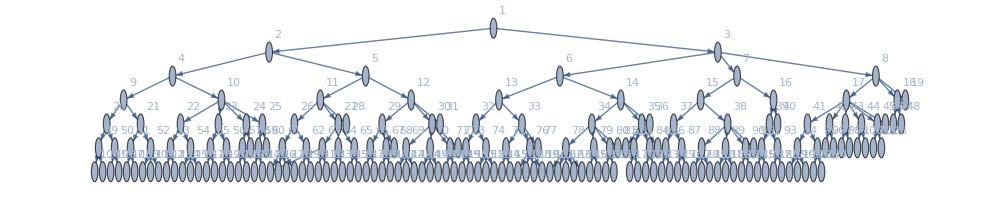

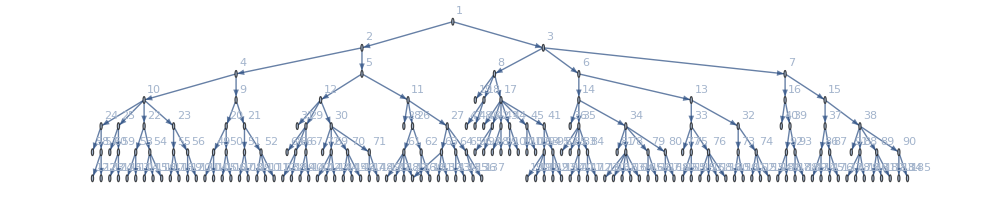

```mathematica
Graph[treeGr,GraphLayout->{"LayeredEmbedding"},VertexLabels->"Index",ImageSize->1000]
Graph[treeGr,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Index",ImageSize->1000]
```

```mathematica
Dynamic[Graph[treeGr,GraphLayout->{"RadialEmbedding"},VertexLabels->"Index",ImageSize->900]]
```

```mathematica
Cases[treeGr,x_->x_]//Length
```

0

```mathematica
procGraph=MapAt[If[LeafCount[#]>20,newn=ToString[Unique["𝒳"]];Print[newn," = ",#/.Style[xx_,__]:>xx];newn,#]&,{All,1,All}]@(MapAt[Style[#,18,Background->White]&,{{All,1,1},{All,1,2},{All,2}}]@xxxxxxx)
```

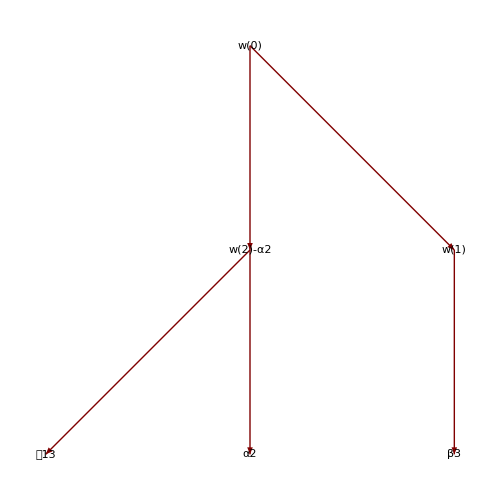

```mathematica
LayeredGraphPlot[procGraph,VertexLabeling->True,EdgeLabeling->Automatic,ImageSize->500]
```

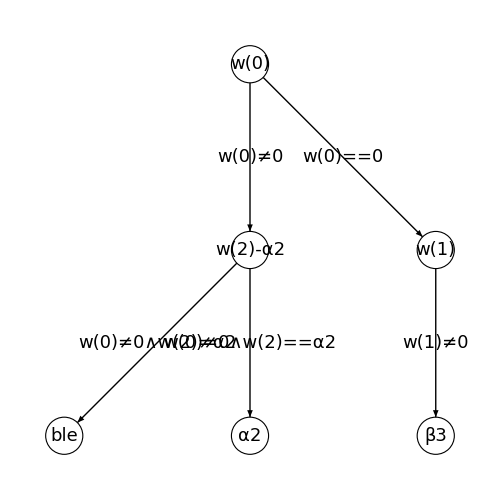

```mathematica
LayeredGraphPlot[assGraph,EdgeRenderingFunction->({Arrow[#1,.1],Inset[Style[#3,18],Mean[#1],Background->White]}&),VertexRenderingFunction->({FaceForm[White],EdgeForm[Black],Disk[#1,.1],Inset[Style[#2,18],#1]}&),ImageSize->500,ImagePadding->{{50,50},{0,0}}]
```

### Testy

```mathematica
M={{a,b,c},{d,e,f},{g,h,i}};
GaussElim[M];
Det[M]
RowReduce[M]//MatrixForm
```

Rank: 3

{{1,0,0},{0,1,0},{0,0,1}}

-c e g+b f g+c d h-a f h-b d i+a e i

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
M=RandomInteger[5,{8,8}];While[Det[M]=!=0,M=RandomInteger[5,{8,8}]]
GaussElim[M]
Det[M]
RowReduce[M]//MatrixForm
```

Rank: 7

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0}}

{{1,1,0,1,0,1,4,4},{0,-1,2,-1,4,-2,-7,-7},{0,0,-1,-3,1,-4,1,0},{0,0,0,-1,3,-6,8,9},{0,0,0,0,-14,31,-36,-44},{0,0,0,0,0,-58,-1068,-1100},{0,0,0,0,0,0,-2150,-2252},{0,0,0,0,0,0,0,0}}

0

(1 | 0 | 0 | 0 | 0 | 0 | 0 | -155/283
0 | 1 | 0 | 0 | 0 | 0 | 0 | -263/283
0 | 0 | 1 | 0 | 0 | 0 | 0 | 547/283
0 | 0 | 0 | 1 | 0 | 0 | 0 | 560/283
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1075/283
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1126/283
0 | 0 | 0 | 0 | 0 | 0 | 1 | -346/283
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
NullSpace[M]/283
NullSpace[%172]
```

{{155/283,263/283,-547/283,-560/283,1075/283,-1126/283,346/283,1}}

{{155/283,263/283,-547/283,-560/283,1075/283,-1126/283,346/283,1}}

```mathematica
NullSpace[%170]/1075
NullSpace[%170.Inverse[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0}}]]/283
```

{{31/215,263/1075,-547/1075,-112/215,283/1075,346/1075,-1126/1075,1}}

{{155/283,263/283,-547/283,-560/283,1075/283,-1126/283,346/283,1}}

```mathematica
M=RandomInteger[5,{6,4}];
GaussElim[M];
RowReduce[M]//MatrixForm
```

Rank: 4

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Q=RandomInteger[{-1,1},{6,6}];
M=Q.{{1,0,3,4,5,6,7},{0,0,0,4,3,1,7},{0,0,0,0,6,6,6},{0,0,0,0,0,0,1},{0,0,0,0,0,0,3},{0,0,0,0,0,0,9}};
GaussElim[M]
RowReduce[M]//MatrixForm
```

Rank: 4

{{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{0,0,0,1,0,0,0}}

{{0,-1,-3,-9,-8,-11,0},{0,0,0,-1,3,5,-4},{0,0,0,0,9,15,-12},{0,0,0,0,0,-36,72},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

(1 | 0 | 3 | 0 | 0 | 3 | 0
0 | 0 | 0 | 1 | 0 | -1/2 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Q=RandomInteger[{-1,1},{6,6}];
M=Q.{{a1,0,3,4,5,6,b7},{0,0,0,c4,3,1,7},{0,0,0,0,6,c6,6},{0,0,0,0,0,0,1},{0,0,0,0,0,0,3},{0,0,0,0,0,0,d9}};
GaussElim[(*MapIndexed[Append[#,{X1,X2,X3,X4,X5,X6}⟦#2⟦1⟧⟧]&,*)M]//MatrixForm
RowReduce[M]//Apart//MatrixForm
```

Rank: 4

{{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{0,1,0,0,0,0,0},{0,0,0,0,1,0,0}}

(0 | 1 | 0 | 0 | 5+d9 | c4 | 3
0 | 0 | -3 | -a1 | 31-b7+7 d9 | -4+6 c4 | 13
0 | 0 | 0 | 0 | 9 | 0 | 0
0 | 0 | 0 | 0 | 0 | -9 c4 c6 | -27 (-2+c6)
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 3/a1 | 0 | 0 | (2 (-2+3 c4))/(a1 c4)-((-12+5 c4) c6)/(6 a1 c4) | 0
0 | 0 | 0 | 1 | 0 | 1/c4-c6/(2 c4) | 0
0 | 0 | 0 | 0 | 1 | c6/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
%200//MatrixForm
```

(0 | 1 | 0 | 0 | 5+d9 | c4 | 3
0 | 0 | -3 | -a1 | 31-b7+7 d9 | -4+6 c4 | 13
0 | 0 | 0 | 0 | 9 | 0 | 0
0 | 0 | 0 | 0 | 0 | -9 c4 c6 | -27 (-2+c6)
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
CellPrint[ExpressionCell[x,"Output"]]
```

x

```mathematica
NullSpace[%201]
```

{{-(-24+36 c4+12 c6-5 c4 c6)/(6 a1 c4),0,0,-(2-c6)/(2 c4),-c6/6,1,0},{-3/a1,0,1,0,0,0,0},{0,1,0,0,0,0,0}}

```mathematica
NullSpace[%200.Inverse[{{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,0,1},{0,1,0,0,0,0,0},{0,0,0,0,1,0,0}}]]
```

{{-(-24+36 c4+12 c6-5 c4 c6)/(6 a1 c4),0,0,-(2-c6)/(2 c4),-c6/6,1,0},{-3/a1,0,1,0,0,0,0},{0,1,0,0,0,0,0}}